This notebook shows Rydberg EIT calculations (velocity dependence) using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134. See the paper for detailed explanation of the technique. 

The code generates Fig. 5 in the paper.

If you use this work for research, we would appreciate citing the paper.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

Install the packages MaTeX and CustomTicks to properly generate the figures:

```mathematica
<<MaTeX`
```

```mathematica
Get["CustomTicks`"]
```

************************************************************************************

Notational definitions

vectorization:  want to represent the N×N density matrix as a N^2 column vector

let v(A)=|A)=∑_ij A_ij i⊗j=∑_ij A_ij i j
Example:  two-level atom ρ=ρ_ee | ρ_eg
ρ_ge | ρ_gg->v(ρ)=ρ_ee
ρ_eg
ρ_ge
ρ_gg

```mathematica
<<Notation`
```

```mathematica
v[A_]:=Flatten[A]
```

Define ⊗ as Kronecker product of x and y:

```mathematica
ClearAll[CircleTimes];

CircleTimes[x_,y_]:=KroneckerProduct[x,y];
```

Define the symbol 𝕀_n as the n by n Identity matrix:

```mathematica
ClearAll[𝕀];
Subscript[𝕀,n_]:=IdentityMatrix[n];
```

Define ᵀ as transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"ᵀ"]]⟹ParsedBoxWrapper[RowBox[{"Transpose","[",x,"]"}]]];
```

Define † as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"†"]]⟹ParsedBoxWrapper[RowBox[{"ConjugateTranspose","[",x,"]"}]]];
```

Define | ⟩ as a column vector, a ket:

```mathematica
ClearAll[Ket];

Ket[v_List]:=Transpose[{Flatten[v]}];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

************************************************************************************
Analytic solution of the steady state (at zero velocity) using Mathematica’s nullspace

-Graphics-

Lets study a system with four energy levels: s, p, d, and f at zero modulation frequency, for which an exact analytic solution can be found (the case of time modulation is studied in another Mathematica notebook).

```mathematica
s={0,0,0,1};p={0,0,1,0};d={0,1,0,0};f={1,0,0,0};
```

```mathematica
H=-Δ p⊗pᵀ-δ d⊗dᵀ-δ f⊗fᵀ+Subscript[ϵ, 1]/2(s⊗SuperDagger[p]+p⊗SuperDagger[s])+Subscript[ϵ, 3]/2(f⊗Transpose[d]+d⊗Transpose[f])+Subscript[ϵ, 2]/2(p⊗Transpose[d]+d⊗Transpose[p])
```

{{-δ,ϵ_3/2,0,0},{ϵ_3/2,-δ,ϵ_2/2,0},{0,ϵ_2/2,-Δ,ϵ_1/2},{0,0,ϵ_1/2,0}}

```mathematica
L=Sqrt[Γ]s⊗Transpose[p];
```

```mathematica
ℒ=-I(H⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Hᵀ)+( L⊗L-1/2 Lᵀ.L⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗Lᵀ.L);
```

Define the trace function for four energy levels:

```mathematica
tr4[A_]:=SuperDagger[v[Subscript[𝕀, 4]]].A
```

The steady state solution is simply the Nullspace of the Hamiltonian H:

```mathematica
steadystate4[G_]:=Module[{rho=Flatten@NullSpace[G]},rho/tr4[rho]];
```

```mathematica
rho4=steadystate4[ℒ];
```

Check that rho4 is normalized (its trace should be one):

```mathematica
SuperDagger[v[Subscript[𝕀, 4]]].rho4//FullSimplify
```

1

Define the coherence ρsp whose imaginary part is proportional to the absorption spectrum χ:

```mathematica
rhosp4[del_,gamma_,Del_,ϵ1_,ϵ2_,ϵ3_]:=SuperDagger[v[s⊗p]].rho4/.{δ->del,Γ->gamma,Δ->Del,Subscript[ϵ, 1]->ϵ1,Subscript[ϵ, 2]->ϵ2,Subscript[ϵ, 3]->ϵ3}
```

This gives the exact steady state solution at zero velocity. To generate the velocity dependence, we just need to Doppler shift the one- and two-photon detunings as Δ->Δ-k_1 v and δ->δ-k_2 v.

```mathematica
vt=169.47351282172082; (*thermal velocity*)
```

```mathematica
k1=1/(.78);(*in micrometer, D2 780 nm transition*)
```

```mathematica
k2=(1/(.78)-1/(.48)); (*two photon transition from ground state to Rydberg*)
```

************************************************************************************

The present method to generate the entire steady-state velocity dependence

See the paper and other codes for details about the theory and numerical implementation of the technique.

-Graphics-
-Graphics-

Define the Lindbladian for certain choice of system parameters at zero velocity.

```mathematica
ℒ0=ℒ/.{Δ->0.,δ->0.,Γ->6.,Subscript[ϵ, 1]->2.,Subscript[ϵ, 2]->1.,Subscript[ϵ, 3]->1.};
ρnullspace=Flatten[NullSpace[ℒ0]];(*Find the nullspace vector, which is proportional to the steady state*)
Traceρnullspace=tr4[ρnullspace];(*Find the trace*)
ρ∞=ρnullspace/Traceρnullspace;(*Divide the nullspace vector by the trace to normalize the steady state solution*)
```

Next, we use the present method to generate the entire velocity dependence by the diagonalization of ℒ_0 and ℒ_0^-ℒ_1 (see the paper and other notebooks for more explanation).

ℒ_0^-=∑_(g≠0) 1/g R_g⊗(L^T)_g 
To construct ℒ_0^- efficiently, we denote R_-=(R_1 R_2...R_(N-1)), where R_g is the column right eigenvector with length N, and L_-=(L_1 L_2...L_(N-1)), where L_g is the column left eigenvector with length N. Let G_-=(g_1 g_2... g_(N-1)) be the list of eigenvalues. The minus subscript in R_-, L_-, and G_- denotes that we are excluding the zero eigenvalues and vectors from these objects.  An equivalent way to rewrite ℒ_0^- is then

ℒ_0^-=(1/(G_-)R_- ).(L_-)^T (normal version)

Here 1/(G_-)R_- denotes the elementwise division: (R_1/g_1 R_2/g_2...(R_(N-1))/(g_(N-1))) while the dot denotes normal matrix multiplication. In Mathematica, the output of eigensystem are rows not columns. Therefore, in Mathematica it is be given by

ℒ_0^-=(1/(G_-)R_- )^T.L_-   (Mathematica version)

Method 2) Using an inverse identity:

We note that ℒ_0^- can be directly constructed as

ℒ_0^-=(ℒ_0+ (R_0 L_0^T))^-1-R_0 L_0^T

i.e., add the nullspace projector P_0=R_0 L_0^T, take the inverse, and then subtract P_0 again. This completely avoids explicit diagonalization and construction of right/left eigenvectors.

```mathematica
P0=SparseArray[KroneckerProduct[ρ∞,Transpose[v[Subscript[𝕀, Length[H]]]]]];
```

```mathematica
(*xsucc=LinearSolve[ℒSparse0,SparseP0];*)
```

```mathematica
ℒ0minus=Inverse[ℒ0+P0]-P0;
```

Next, we construct the auxiliary Lindbladian ℒ_1:

```mathematica
ℒ1=D[ℒ/.{Δ->0.-k1 vel,δ->0.-k2 vel,Γ->6.,Subscript[ϵ, 1]->2.,Subscript[ϵ, 2]->1.,Subscript[ϵ, 3]->1.},vel];
```

Now diagonalize the auxiliary problem to find the Propagator:

```mathematica
{λ,rλ}=Eigensystem[ℒ0minus.ℒ1];(*Find the right eigenvectors and eigenvalues of Subscript[ℒ, 0]^-Subscript[ℒ, 1]*)
```

```mathematica
Lλ=PseudoInverse[Transpose[rλ]];(*Construct the left eigenvectors out of the right eigenvectors*)
```

The eigenvalues from 27 to 64 here are effectively zero:

The entire velocity dependence is given by

 ρ_v=(∑_λ 1/(1+λ v)r_λ⊗l_λ)ρ_0
 
 which can be efficiently constructed as 

ρ_v={(1/(1+v Λ)r)^T.l}.ρ_0 

where r=(r_1 r_2...r_N) is the right eigenvectors of ℒ_0^-.ℒ_1 and l=(l_1 l_2...l_N) are the left eigenvectors and Λ=(λ_1 λ_2... λ_N) are the eigenvalues. 1/(1+v Λ)r is an elementwise division between Λ and r while the dot denotes matrix multiplication.

Define the steady state as a function of velocity:

```mathematica
ρv[v_]:=(Transpose[(1/(1+v λ))rλ].Lλ).ρ∞;
```

This generates the exact velocity dependence, generated from the propagator acting on the zero-velocity steady state solution. Below, we compare this solution vs the exact solution vs perturbation theory.

**********************************************************************
Perturbation theory to generate the velocity dependence:

-Graphics-
-Graphics-

Perturbation theory up to the second order gives:

ρ_v∼ [I-v ℒ_0^-ℒ_1+v^2 (ℒ_0^-ℒ_1)^2]ρ_0 

ρ_v∼ ∑_n (-v ℒ_0^-ℒ_1)^n ρ_0  for any order n.

In the eigenbasis of ℒ_0^-ℒ_1, this is given by (Transpose[ λ rλ].Lλ) [Mathematica’s definition]:

```mathematica
ρv2ndorder[v_]:=(Subscript[𝕀, 16]-v(Transpose[ λ rλ].Lλ)+v^2 MatrixPower[((Transpose[ λ rλ].Lλ)),2]).ρ∞;
```

```mathematica
ρv2ndordernormalize[v_]:=ρv2ndorder[v]/tr4[ρv2ndorder[v]]//Chop
```

**********************************************************************
Present solution vs exact solution vs second order perturbation

Now compare the present solution vs the exact solution vs perturbation theory as in generating the steady state as a function of v/v_th:

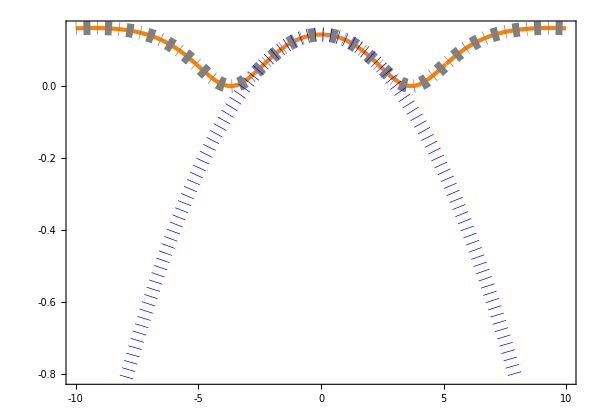

```mathematica
Plot1=Plot[{Evaluate[Im[SuperDagger[v[s⊗p]].ρv[vel]/.{vel-> x vt}]],Evaluate[{Im[rhosp4[0.-k2 vel,6.,0.-k1 vel,2.,1.,1.]/.{vel->x vt}]}],Evaluate[Im[SuperDagger[v[s⊗p]].ρv2ndordernormalize[vel]/.{vel->x vt}]]},{x,-0.01,0.01},FrameLabel->{MaTeX["v/v_{\\rm th}\\ (\\text{\\scriptsize \\(\\times 10^{-3}\\)}) ",Magnification->3],MaTeX["\\text{Im}(\\rho_{\\rm sp}) ",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks[-0.01,0.01,TickLabelFunction->(Rationalize[#/10^-3]&)],LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->600,Axes->False,PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0,0}],{0.6,0.3}],PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]],Directive[Blue,Dotted,AbsoluteThickness[10]]},LabelStyle->{FontSize->30,FontFamily->"Times New Roman"},AspectRatio->0.7]
```

Compare the present solution vs exact solution for larger range of the velocity:

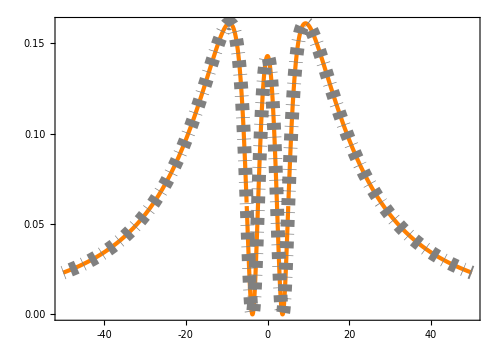

```mathematica
Plot2=Plot[{Evaluate[Im[SuperDagger[v[s⊗p]].ρv[vel]/.{vel->x vt}]],Evaluate[{Im[rhosp4[0.-k2 vel,6.,0.-k1 vel,2.,1.,1.]/.{vel->x vt}]}]},{x,-0.05,0.05},FrameLabel->{MaTeX["v/v_{\\rm th} \\ (\\text{\\scriptsize \\(\\times 10^{-3}\\)}) ",Magnification->3],MaTeX["\\text{Im}(\\rho_{\\text{sp}}) ",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks[-0.05,0.05,TickLabelFunction->(Rationalize[#/10^-3]&)],LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]],Directive[Blue,Dotted,AbsoluteThickness[10]]},LabelStyle->{FontSize->30,FontFamily->"Times New Roman"},AspectRatio->0.7,PlotLegends->Placed[LineLegend[{"","",""},LegendMarkerSize->{0,0}],{0.5,0.2}],PlotPoints->100]
```

Compare the present solution vs exact solution for an even larger range of the velocity:

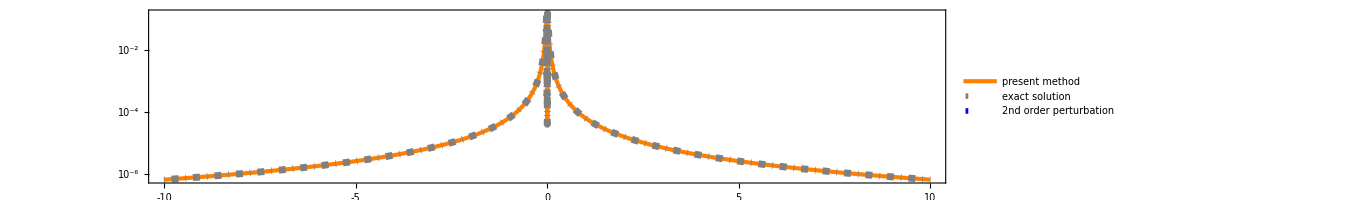

```mathematica
Plot3=Plot[{Evaluate[Log10[Im[SuperDagger[v[s⊗p]].ρv[vel]/.{vel->x vt}]]],Evaluate[{Log10[Im[rhosp4[0.-k2 vel,6.,0.-k1 vel,2.,1.,1.]/.{vel->x vt}]]}],I},{x,-10,10},FrameLabel->{MaTeX["v/v_{\\rm th}",Magnification->3],MaTeX["\\text{Im}(\\rho_{\\rm sp}) ",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],GridLines->None,ImageSize->1000,PlotRange->All,FrameTicks->{{LogTicks[-6,-1,TickLabelStep->2],None},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},Axes->False,PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[5]],Directive[Blue,Dotted,AbsoluteThickness[20]]},LabelStyle->{FontSize->25,FontFamily->"Times New Roman"},AspectRatio->0.2,PlotLegends->Placed[LineLegend[{"present method","exact solution","2nd order perturbation"},LegendMarkerSize->{40,20}],{0.8,0.6}],PlotPoints->1000]
```

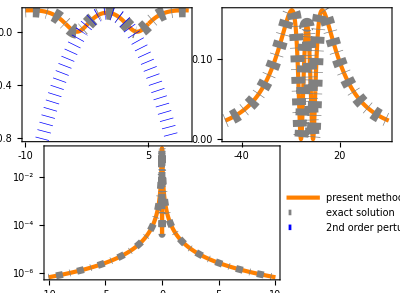

```mathematica
GraphicsGrid[{{Plot1,Plot2},{Plot3,SpanFromLeft}},ImageSize->Full,Spacings->{0,-50},Alignment->Center,ImagePadding->{{Automatic,Automatic},{155,Automatic}}]
```